```mathematica
(* Riemannian three attractor model {0,1,Infinity} on Pioncare disk with Cauchy wave function: long tailed distribution*)
```

```mathematica
(*Cauchy wave function*)
```

```mathematica
Clear[Ψ,Ψ0,r]
```

```mathematica
Ψ[r_]=Ψ0/(1+r^2)
```

Ψ0/(1+r^2)

```mathematica
(*Normalization*)
```

```mathematica
w=Integrate[Ψ[r],{r,0,Infinity}]
```

(π Ψ0)/2

```mathematica
Ψ0=2/Pi
```

2/π

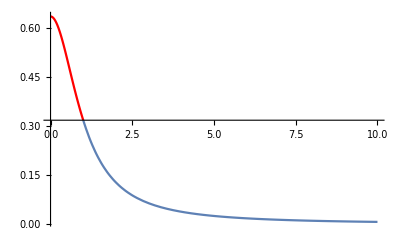

```mathematica
g0=Show[{Plot[Ψ[r],{r,0,1},PlotStyle->Red,PlotRange->All],Plot[Ψ[r],{r,1,10},PlotRange->All]},PlotRange->All]
```

```mathematica
Integrate[Ψ[r],{r,0,r0}]+Integrate[Ψ[r],{r,r0,Infinity}]
```

ConditionalExpression[1, -1<Im[r0]<0||0<Im[r0]<1||Re[r0]≠0]

```mathematica
Reduce[Integrate[Ψ[r],{r,0,r0}]==Integrate[Ψ[r],{r,r0,Infinity}],r0]
```

r0==1

```mathematica
(*Einstein Ricci scalar energy density: R1=-8*Pi*G/c^4*Te*)
```

```mathematica
(*exterior elliptic energy density:R2=8*Pi*G/c^4*Te *)
```

```mathematica
(*such that R1+R2=0: matter and energy of curvatures are equal*)
```

```mathematica
(* Ricci scalar curvature for hyperbolic Minkowsky manifold*)
R1=-3!/r^2
```

-6/r^2

```mathematica
Te=R1/(8*Pi*G/c^4)
```

-(2.89001×10^48)/r^2

```mathematica
(* Ricci scalar curvature for Elliptic manifold*)
```

```mathematica
R2=3!/r^2
```

6/r^2

```mathematica
(* Hyerbolic Minkowski-Einstein Universe as a disk of radius ra integrated over the radius: radial density*)
```

```mathematica
Integrate[R1,{r,0,ra}]
```

Integrate::idiv: Integral of -6/r^2 does not converge on {0,ra}.

∫_0^ra -6/r^2ⅆr

```mathematica
(* ellitic exterior of  Universe as a disk of radius ra integrated over the radius:radial density*)
```

```mathematica
Integrate[R2,{r,ra,Infinity}]
```

ConditionalExpression[6/ra, Im[ra]≠0||Re[ra]>0]

```mathematica
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2
```

4.4×10^28

```mathematica
(3*c^2)/G
```

4.04081×10^28

```mathematica
(* 1=2*M*G/(c^2*ra) singular blackhole*)
```

```mathematica
1/r/.Solve[ 1==2*M*G/(c^2*r) /.M->1,r][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

6.73468×10^27

```mathematica
6.734680077277472*^27/((c^2)/(2*G))
```

1.

```mathematica
(* setting the radial densities equal*)
```

```mathematica
ra1=ra/.FindRoot[-Integrate[R1,{r,0,ra}]==-6/ra,{ra,(c^2)/(2*G)}][[1]]
```

Integrate::idiv: Integral of -6/r^2 does not converge on {0,ra}.

Integrate::idiv: Integral of -6/r^2 does not converge on {0,6.73468×10^27}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.05416×10^-29}. NIntegrate obtained -1.53216×10^130 and 1.53216×10^130 for the integral and error estimates.

Integrate::idiv: Integral of -6/r^2 does not converge on {0,ra}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ra} = {6.73468×10^27}. Try perturbing the initial point(s).

6.73468×10^27

```mathematica
(*Weyl gauge gravity constant*)
```

```mathematica
G0=hbar*c/e
```

6.58212×10^-8

```mathematica
(c^2)/(2*G0)
```

6.82724×10^27

```mathematica
e*c/(2*hbar)
```

6.82724×10^27

```mathematica
ra2=ra/.FindRoot[-Integrate[R1,{r,0,ra}]==-6/ra,{ra,(c^2)/(2*G0)}][[1]]
```

Integrate::idiv: Integral of -6/r^2 does not converge on {0,ra}.

Integrate::idiv: Integral of -6/r^2 does not converge on {0,6.82724×10^27}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.06864×10^-29}. NIntegrate obtained -1.51139×10^130 and 1.51139×10^130 for the integral and error estimates.

Integrate::idiv: Integral of -6/r^2 does not converge on {0,ra}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {ra} = {6.82724×10^27}. Try perturbing the initial point(s).

6.82724×10^27

```mathematica
ra2/ra1
```

1.01374

```mathematica
ru/(2*Pi*ra1)
```

1.03981

```mathematica
(*Radial density of the universe*)
```

```mathematica
(6/ru)/(8*Pi*G/c^4)
```

```mathematica
1/(6.56821×10^19)
```

```mathematica
1.5224848170201624*^-20/mH
```

67.663

```mathematica
Hcbm=67.4
```

```mathematica
Hsnova=74.8
```

```mathematica
Solve[Hcbm/Hsnova==v/c,v]
```

{{v→2.73054×10^10}}

```mathematica
e=Sqrt[1-(Hcbm/Hsnova)^2]
```

0.412824

```mathematica
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
```

```mathematica
ru/(Pi*c*tu)
```

1.07291

```mathematica
(*Jacobian -Lorentz function for age of the universe*)
```

```mathematica
Integrate[1/Sqrt[(1-e^2*t^2)*(1-t^2)],{t,0,tu}]
```

1.65054+2.33027 ⅈ

```mathematica
Integrate[(1-e^2*t^2)*(1-t^2),{t,0,1}]/(Log[2]/Log[3])
```

1.02063

```mathematica
(*Jacobian-Lorentz unitary function*)
```

```mathematica
(*Mexican hat false vacuum*)
```

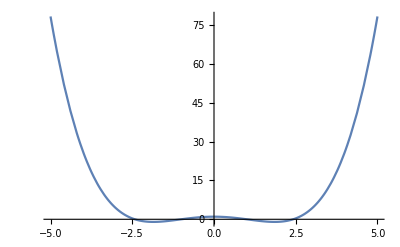

```mathematica
Plot[(1-e^2*t^2)*(1-t^2),{t,-5,5}]
```

```mathematica
Solve[D[(1-e^2*t^2)*(1-t^2),{t,1}]==0,t]
```

{{t→-1.85307},{t→0.},{t→1.85307}}

```mathematica
Integrate[1/Sqrt[(1-e^2*t^2)*(1-t^2)],{t,-1.8530690259817455,1.8530690259817455}]
```

```mathematica
(3.290023013047149-2.940140817266687 ⅈ)/(Pi-I*Pi)
```

0.991561+0.0556855 ⅈ

```mathematica
2.940140817266687/3.290023013047149
```

0.893654

```mathematica
Hcbm/Hsnova
```

0.910811

```mathematica
Abs[(3.290023013047149-2.940140817266687 ⅈ)]/Abs[(Pi-I*Pi)]
```

0.993124

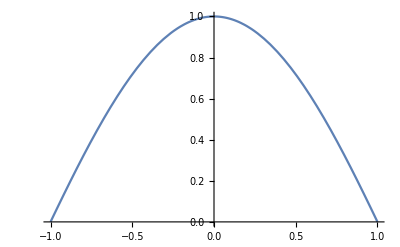

```mathematica
g1=Plot[(1-e^2*t^2)*(1-t^2),{t,-1,1}]
```

```mathematica
(*Close to a stretched cosine wave*)
```

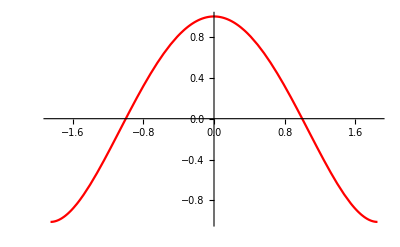

```mathematica
g2=Plot[(1-e^2*t^2)*(1-t^2),{t,-1.8530690259817455,1.8530690259817455},PlotStyle->Red]
```

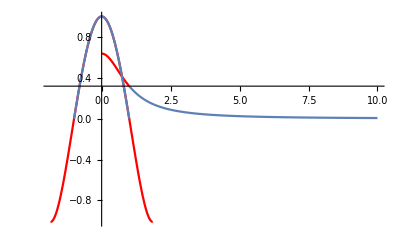

```mathematica
Show[{g0,g2,g1}]
```

```mathematica
Tvac=2.72548;
```

```mathematica
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
```

```mathematica
Solve[k0*Pi^2*Tvac/(Sqrt[3]*α*hbar^2)-(ru^2-ra1^2)==0,k0]
```

{{k0→0.987975}}

```mathematica
Plot[Pi^2*Tvac/(Sqrt[3]*α*hbar^2)-(ru^2-r^2),{r,0,ru}]
```

-Graphics-

```mathematica
Plot[(1-(r/ru)^2),{r,-ru,ru}]
```

-Graphics-

```mathematica
Plot[((ru/ra1)^2-(r/ra1)^2)/42.2,{r,0,ru}]
```

-Graphics-